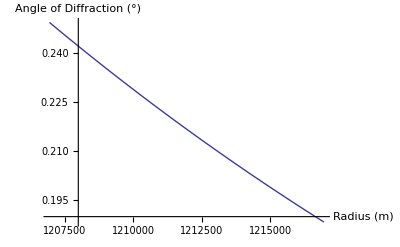

```mathematica
Clear["Global`*"];

mPluto = 1.29*10^22; (*kg; mass of Pluto from Elliot et al. 1989*)

mu = .02; (*kg/mol; mean molecular weight of atmosphere from NASA factsheet*)
g = 0.583; (*m/s^2; surface gravity of Pluto*)
R=8.3145; (*J/mol K; universal gas constant*)
T = 50; (* Kelvin; assumed constant, following NASA factsheet, for now*)
rSurf = 1195000; (*meters; surface radius of Pluto*)
DPluto = 4.864*10^12;  (*meters; current distance from Earth to Pluto*)

r0 = rSurf*1.01; (*reference radius*)
a=(mu*g)/(R*T); (*inverse scale height*)
n0 = 1.00029839; (*reference refractive index @ surface, for now*)
rSurf = 100;

θ=(2*Pi*r0*a)^(1/2)*(n0-1)*E^(-a*(r-r0));
θdeg = θ/(2*Pi)*360;
Plot[θdeg,{r,r0,r0+10000},AxesLabel-> {"Radius (m)", "Angle of Diffraction (°)"}]
(* looks like this angle is parameterized to the angle of refraction at r0? *)
```

```mathematica
Clear["Global`*"];
(*Manipulate[((phiRatio-2)+Log[phiRatio-1])/(Subscript[a, Δ]*Subscript[v, Δ]),{*)
(*a=0.00002790306091767394;*)
v = 12000;
Solve[((phiRatio-2)+Log[phiRatio-1])==(a*v*t),phiRatio]
Manipulate[Plot[1+ProductLog[E^(1+(a*v*t))],{t,0,120},AxesLabel-> {"time (s)","flux ratio"}],{a,0.000025,0.000030}]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{phiRatio→1+ProductLog[ⅇ^(1+12000 a t)]}}

Plot::exclul: {ⅇ^1 + 0.000025` Re[Times[« 2 »]] Sin[0.000025` Im[t v]] - 0} must be a list of equalities or real-valued functions.